```mathematica
Reduce[{-1≤i≤1,-1≤j≤1,-1≤2-i≤1,-1≤j+2≤1},Integers]
```

j==-1&&i==1

```mathematica
Reduce[{(a+i)(b)<(b+j+1)(a+1),a>0,b>0,-1≤i≤1,-1≤j≤1},Integers]
```

((a|b)∈Integers&&a≥1&&b≥1&&i==-1&&j==-1)||((a|b)∈Integers&&a≥1&&b≥1&&i==-1&&j==0)||((a|b)∈Integers&&a≥1&&b≥1&&i==-1&&j==1)||((a|b)∈Integers&&a≥1&&b≥1&&i==0&&j==-1)||((a|b)∈Integers&&a≥1&&b≥1&&i==0&&j==0)||((a|b)∈Integers&&a≥1&&b≥1&&i==0&&j==1)||((a|b)∈Integers&&a≥1&&b≥1&&i==1&&j==0)||((a|b)∈Integers&&a≥1&&b≥1&&i==1&&j==1)

```mathematica
Refine[Reduce[{
dp1>0,dm1>0,dp2>0,dm2>0,
-1≤i≤1,-1≤j≤1,

dp1+i==dm1,
dp2==dm2+j,

dp3==dp1+1,
dm3==dm1-1,

dp4==dp2-1,
dm4==dm2+1,

-1≤dp1-dm1≤1,
-1≤dp2-dm2≤1,

-1≤dp3-dm3≤1,
-1≤dp4-dm4≤1

},{i,j},Integers],(dm1|dm2)∈Integers]
```

(C[1]|C[2])∈Integers&&C[1]≥0&&dm2==1+C[1]&&dm4==2+C[1]&&dp2==2+C[1]&&dp4==1+C[1]&&C[2]≥0&&dm1==2+C[2]&&dm3==1+C[2]&&dp1==1+C[2]&&dp3==2+C[2]&&i==1&&j==1

```mathematica
"This is the only possible case where the flip leaves COND1 intact."
```

```mathematica
Refine[Reduce[{
dp1>0,dm1>0,dp2>0,dm2>0,

dp1+1==dm1,
dp2==dm2+1,

dp3==dp1+1,
dm3==dm1-1,

dp4==dp2-1,
dm4==dm2+1,

-1≤dp1-dm1≤1,
-1≤dp2-dm2≤1,

-1≤dp3-dm3≤1,
-1≤dp4-dm4≤1,

(dp1*dm2<dm3*dp4)∨(dp1*dm2>dm3*dp4)
},Integers],(dm1|dm2)∈Integers]
```

False

```mathematica
"And this case guarantees the same number of paths."
```

```mathematica
Refine[Reduce[{
dp1>0,dm1>0,dp2>0,dm2>0,
-1≤i≤1,-1≤j≤1,

dp1+i==dm1,
dp2==dm2+j,

dp3==dp1+1,
dm3==dm1-1,

dp4==dp2-1,
dm4==dm2+1,

-1≤dp1-dm1≤1,
-1≤dp2-dm2≤1,

¬((-1≤dp3-dm3≤1)∧(-1≤dp4-dm4≤1)),

dp1*dm2≤dm3*dp4
},{i,j},Integers],(dm1|dm2)∈Integers]
```

False

```mathematica
"If COND1 is removed by flipping the edge, the number of actual paths is greater than the number of potential paths."
```

```mathematica
Normal[AdjacencyMatrix[Graph[{1<->2,
1<->3,
1<->7,
2<->3,
2<->4,
3<->5,
4<->6,
4<->7,
5<->6,
5<->7,
6<->7},VertexLabels->"Name"]]]//MatrixForm
```

```mathematica
f0[{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_}]:=({{0, a, b, c, 0, 0, 0}, {1-a, 0, d, 0, e, 0, 0}, {1-b, 1-d, 0, 0, 0, f, 0}, {1-c, 0, 0, 0, g, h, i}, {0, 1-e, 0, 1-g, 0, 0, j}, {0, 0, 1-f, 1-h, 0, 0, k}, {0, 0, 0, 1-i, 1-j, 1-k, 0}})
f[n_]:=Length[FindCycle[AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],11]]],∞,All]]
f[0]
```

0

```mathematica
h[n_]:=AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],11]]]
```

```mathematica
c[n_]:=Boole[CondQ[AdjacencyGraph[f0[PadLeft[IntegerDigits[n,2],11]]]]]
```

```mathematica
SetSharedVariable[counter];
counter=0;
Monitor[ParallelTable[If[counter<n,counter=n];f[n],{n,1,2^11}],counter]
```

{0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,1,0,3,1,3,0,1,3,3,3,3,3,3,1,0,0,3,1,1,0,3,0,0,1,3,3,0,0,1,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,1,0,0,3,3,1,0,0,3,0,1,1,3,0,0,1,3,3,3,3,3,3,1,0,3,1,3,0,1,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,5,2,3,0,2,5,2,3,6,6,4,2,1,1,5,2,5,2,7,1,3,5,6,5,6,5,7,3,0,0,0,0,3,2,1,0,0,3,0,1,2,4,0,0,1,1,3,2,3,2,3,1,1,3,2,3,2,3,1,1,0,0,1,0,5,1,5,0,3,5,5,5,7,5,7,3,0,0,5,1,3,0,7,0,2,3,7,5,4,2,7,2,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,5,3,2,0,1,5,1,2,5,7,2,1,2,2,5,3,6,4,6,2,3,6,5,5,6,7,5,3,0,1,0,0,5,5,1,0,0,5,0,1,3,7,0,0,3,5,5,5,7,7,5,3,2,7,3,5,4,7,2,2,0,0,0,0,3,1,2,0,1,3,1,2,3,3,2,1,0,0,3,1,2,0,4,0,1,2,3,3,2,1,3,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,1,1,1,3,2,2,1,1,3,1,2,2,3,1,1,1,1,3,2,2,1,3,1,1,2,2,3,1,1,1,1,2,5,2,3,5,6,3,2,1,6,1,3,2,5,1,1,3,6,5,6,5,5,5,3,1,5,2,5,1,2,1,1,2,2,5,3,5,3,6,2,3,5,6,6,5,5,5,3,1,1,6,3,2,1,5,1,1,2,5,5,1,1,2,1,3,5,5,5,5,5,5,3,2,6,3,5,3,5,2,2,2,3,6,5,3,2,5,2,1,3,3,5,1,1,1,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,5,1,2,5,7,2,1,0,6,0,2,1,5,0,0,3,8,5,7,6,7,5,3,0,6,1,5,0,2,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,3,1,2,3,3,2,1,0,4,0,2,1,3,0,0,1,2,3,3,2,1,3,1,0,2,1,3,0,0,0,0,1,1,1,1,5,3,3,1,2,5,2,3,5,6,3,2,2,2,5,3,5,3,6,2,3,5,5,5,5,5,5,3,1,2,1,1,5,5,2,1,1,5,1,2,3,6,1,1,3,5,5,5,6,6,5,3,2,6,3,5,3,5,2,2,1,1,2,1,5,2,5,1,3,5,5,5,6,5,6,3,1,1,5,2,3,1,6,1,2,3,6,5,3,2,5,2,1,1,1,1,3,2,2,1,1,3,1,2,2,3,1,1,1,1,3,2,2,1,3,1,1,2,2,3,1,1,1,1,0,0,0,0,3,2,1,0,0,3,0,1,2,4,0,0,1,1,3,2,3,2,3,1,1,3,2,3,2,3,1,1,0,2,0,0,5,6,1,0,0,5,0,1,2,6,0,0,3,7,5,6,7,8,5,3,1,7,2,5,2,5,1,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,1,5,2,5,2,7,1,3,5,8,7,6,5,7,3,0,0,6,2,1,0,5,0,0,1,6,5,0,0,2,0,1,1,3,2,3,2,3,1,1,3,2,3,2,3,1,1,0,0,4,2,1,0,3,0,0,1,2,3,0,0,0,0,1,1,1,1,3,2,2,1,1,3,1,2,2,3,1,1,1,1,3,2,2,1,3,1,1,2,2,3,1,1,1,1,2,5,2,3,5,6,3,2,1,6,1,3,2,5,1,1,3,6,5,6,5,5,5,3,1,5,2,5,1,2,1,1,2,2,5,3,5,3,6,2,3,5,6,6,5,5,5,3,1,1,6,3,2,1,5,1,1,2,5,5,1,1,2,1,3,5,5,5,5,5,5,3,2,6,3,5,3,5,2,2,2,3,6,5,3,2,5,2,1,3,3,5,1,1,1,1,0,0,0,0,3,1,2,0,1,3,1,2,3,3,2,1,0,0,3,1,2,0,4,0,1,2,3,3,2,1,3,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,2,0,5,1,6,0,3,5,7,6,7,5,8,3,0,0,5,1,2,0,6,0,1,2,7,5,2,1,5,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,1,1,1,5,3,3,1,2,5,2,3,5,6,3,2,2,2,5,3,5,3,6,2,3,5,5,5,5,5,5,3,1,2,1,1,5,5,2,1,1,5,1,2,3,6,1,1,3,5,5,5,6,6,5,3,2,6,3,5,3,5,2,2,1,1,2,1,5,2,5,1,3,5,5,5,6,5,6,3,1,1,5,2,3,1,6,1,2,3,6,5,3,2,5,2,1,1,1,1,3,2,2,1,1,3,1,2,2,3,1,1,1,1,3,2,2,1,3,1,1,2,2,3,1,1,1,1,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,1,3,1,2,3,3,2,1,0,4,0,2,1,3,0,0,1,2,3,3,2,1,3,1,0,2,1,3,0,0,0,0,2,2,7,4,5,3,7,2,3,5,7,7,5,5,5,3,0,0,7,3,1,0,5,0,0,1,5,5,0,0,1,0,3,5,7,6,5,5,6,3,2,6,4,6,3,5,2,2,1,2,7,5,2,1,5,1,0,2,3,5,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,2,7,2,4,5,7,3,2,0,7,0,3,1,5,0,0,3,7,5,7,5,5,5,3,0,5,1,5,0,1,0,0,1,1,3,2,3,2,3,1,1,3,2,3,2,3,1,1,0,0,4,2,1,0,3,0,0,1,2,3,0,0,0,0,3,7,5,6,5,6,5,3,1,7,2,5,2,5,1,1,2,4,6,6,3,2,5,2,0,3,2,5,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,1,0,3,1,3,0,1,3,3,3,3,3,3,1,0,0,3,1,1,0,3,0,0,1,3,3,0,0,1,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,1,0,0,3,3,1,0,0,3,0,1,1,3,0,0,1,3,3,3,3,3,3,1,0,3,1,3,0,1,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0,0,0,0,2,1,1,0,0,2,0,1,1,2,0,0,0,0,2,1,1,0,2,0,0,1,1,2,0,0,0,0,0}

```mathematica
Flatten[Position[Out[85],8]]
```

{689,949,1098,1358}

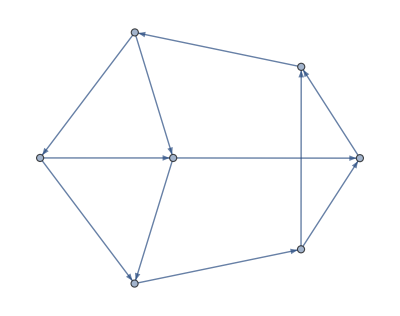
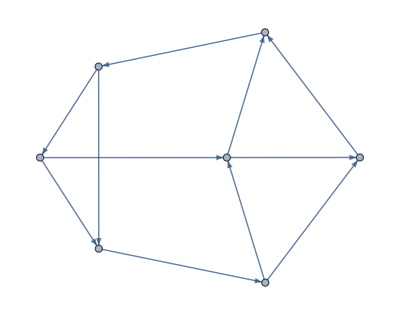
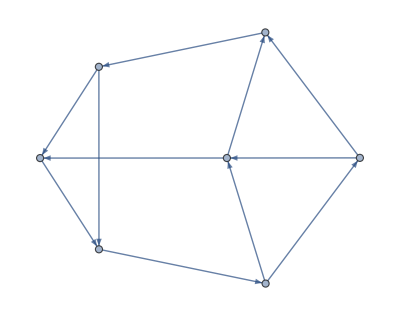
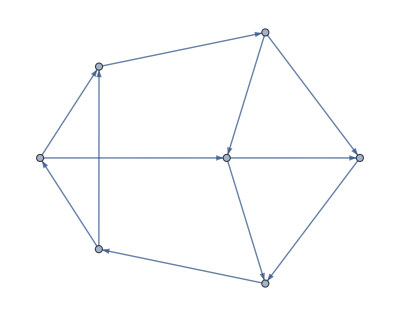

```mathematica
Map[AdjacencyGraph[f0[PadLeft[IntegerDigits[#,2],11]]]&,Flatten[Position[Out[85],8]]]
```

```mathematica
CondQ[graph_]:=And@@Map[Abs[VertexInDegree[graph,#]-VertexOutDegree[graph,#]]<2&,VertexList[graph]]
Map[CondQ,Out[90]]
```

{True,True,True,True}

```mathematica
SetSharedVariable[counter];
counter=0;
Monitor[ParallelTable[If[counter<n,counter=n];c[n],{n,1,2^11}],counter]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten[Position[Out[107],1]]
```

```mathematica
Map[f,{268,269,276,278,281,282,283,332,333,334,342,346,347,396,397,404,406,409,410,411,429,436,437,438,441,443,516,521,530,548,549,553,561,562,563,580,582,585,586,587,594,612,613,614,617,619,626,627,676,677,681,689,690,691,780,781,788,790,793,794,795,813,820,821,822,825,827,844,845,846,854,858,859,877,886,891,941,948,949,950,953,955,1092,1094,1097,1098,1099,1106,1156,1161,1170,1188,1189,1193,1201,1202,1203,1220,1222,1225,1226,1227,1234,1252,1253,1254,1257,1259,1266,1267,1356,1357,1358,1366,1370,1371,1420,1421,1428,1430,1433,1434,1435,1453,1460,1461,1462,1465,1467,1484,1485,1486,1494,1498,1499,1517,1526,1531,1604,1606,1609,1610,1611,1618,1636,1637,1638,1641,1643,1650,1651,1700,1701,1705,1713,1714,1715,1764,1765,1766,1769,1771,1778,1779}]
```

{6,6,5,7,5,6,5,7,5,7,7,7,5,5,7,6,6,6,5,5,7,7,7,5,7,5,3,3,3,5,6,6,6,5,6,5,6,5,6,6,6,5,5,5,6,5,6,5,5,7,6,8,5,7,5,6,5,6,5,5,5,6,6,6,5,6,5,6,5,6,6,6,5,3,3,3,6,7,8,5,7,5,5,7,5,8,7,6,3,3,3,5,6,6,6,5,6,5,6,5,6,6,6,5,5,5,6,5,6,5,7,5,8,6,7,5,5,6,5,6,5,5,5,6,6,6,5,6,5,6,5,6,6,6,5,3,3,3,5,7,5,7,7,7,5,5,6,6,6,7,5,5,7,7,7,5,7,5,6,5,7,5,6,6}

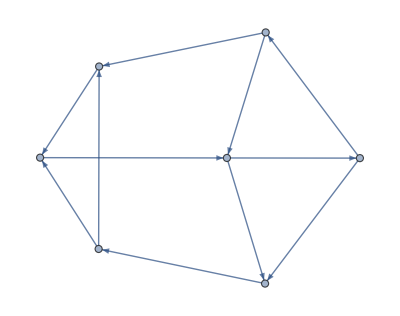

```mathematica
AdjacencyGraph[f0[PadLeft[IntegerDigits[268,2],11]]]
```

```mathematica
{1,2,1}-{1,0,1}
```

{0,2,0}

```mathematica
bitdif11[a0_,b0_]:=Block[{a1=PadLeft[IntegerDigits[a0,2],11],b1=PadLeft[IntegerDigits[b0,2],11]},Total[Map[Abs,a1-b1]]]
```

```mathematica
{689,949,1098,1358}
```

```mathematica
Position[Map[bitdif11[689,#]&,Flatten[Position[Out[107],1]]],1]
```

{{33},{54},{155}}

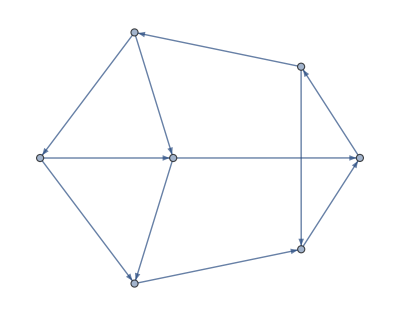
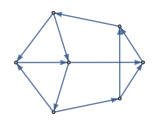
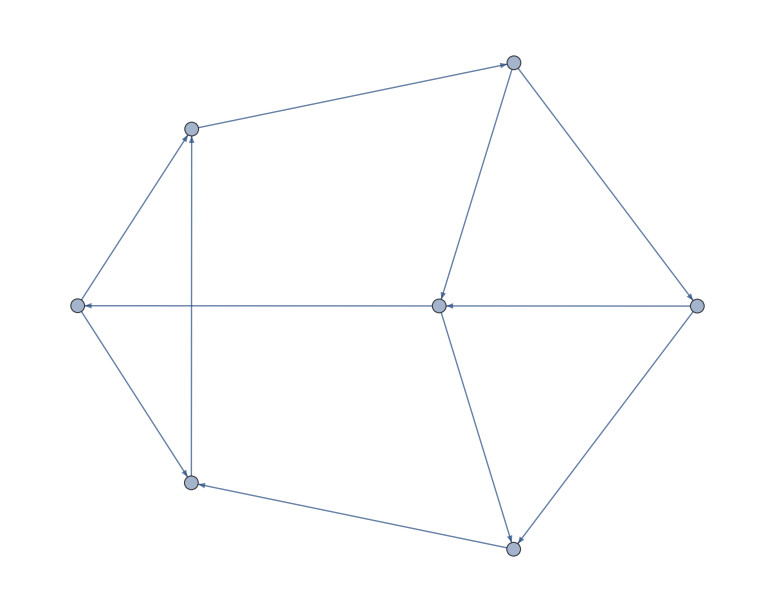
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{h[689],h[Flatten[Position[Out[107],1]][[33]]],h[Flatten[Position[Out[107],1]][[54]]],h[Flatten[Position[Out[107],1]][[155]]]}
```

```mathematica
Map[numcycles,{h[689],h[Flatten[Position[Out[107],1]][[33]]],h[Flatten[Position[Out[107],1]][[54]]],h[Flatten[Position[Out[107],1]][[155]]]}]
```

{8,6,7,7}

```mathematica
numcycles[graph_]:=Length[FindCycle[graph,∞,All]]
```

```mathematica
numcycles[h[Flatten[Position[Out[107],1]][[33]]]]
```

6

```mathematica
Map[Length[FindCycle[h[#],∞,All]]&,Flatten[Position[Out[107],1]]]
```

{6,6,5,7,5,6,5,7,5,7,7,7,5,5,7,6,6,6,5,5,7,7,7,5,7,5,3,3,3,5,6,6,6,5,6,5,6,5,6,6,6,5,5,5,6,5,6,5,5,7,6,8,5,7,5,6,5,6,5,5,5,6,6,6,5,6,5,6,5,6,6,6,5,3,3,3,6,7,8,5,7,5,5,7,5,8,7,6,3,3,3,5,6,6,6,5,6,5,6,5,6,6,6,5,5,5,6,5,6,5,7,5,8,6,7,5,5,6,5,6,5,5,5,6,6,6,5,6,5,6,5,6,6,6,5,3,3,3,5,7,5,7,7,7,5,5,6,6,6,7,5,5,7,7,7,5,7,5,6,5,7,5,6,6}

```mathematica
MatrixForm[Normal[AdjacencyMatrix[WheelGraph[6]]]]
```

```mathematica
Clear[f,h]
```

```mathematica
g0[{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_}]:=({{0, a, b, c, d, e}, {1-a, 0, f, 0, 0, g}, {1-b, 1-f, 0, h, 0, 0}, {1-c, 0, 1-h, 0, i, 0}, {1-d, 0, 0, 1-i, 0, j}, {1-e, 1-g, 0, 0, 1-j, 0}})
g1[n_]:=Length[FindCycle[AdjacencyGraph[g0[PadLeft[IntegerDigits[n,2],10]]],∞,All]]
g2[n_]:=AdjacencyGraph[g0[PadLeft[IntegerDigits[n,2],10]]]
```

```mathematica
Length[Select[Out[169],CondQ[AdjacencyGraph[g0[PadLeft[IntegerDigits[#,2],10]]]]&]]
Length[Out[169]]
```

60

60

```mathematica
Flatten[Position[Table[g1[n],{n,1,2^10}],7]]
```

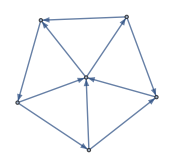
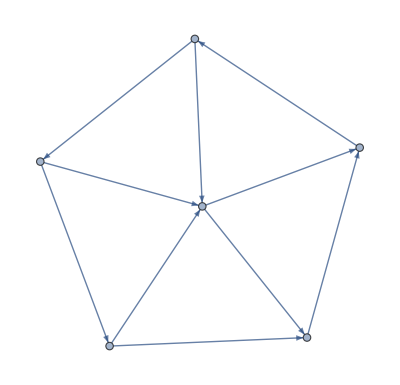
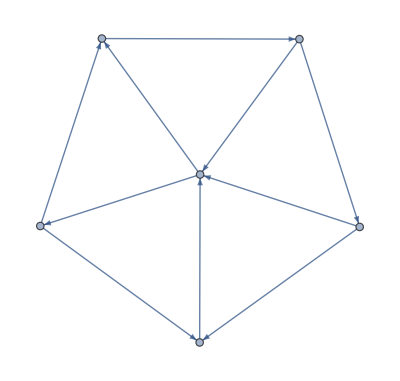
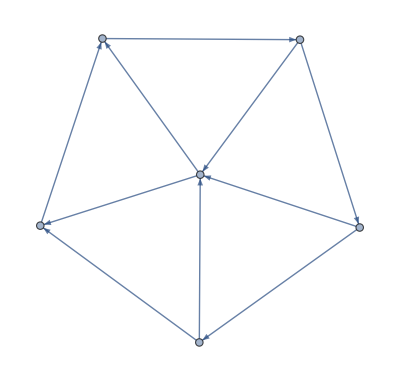
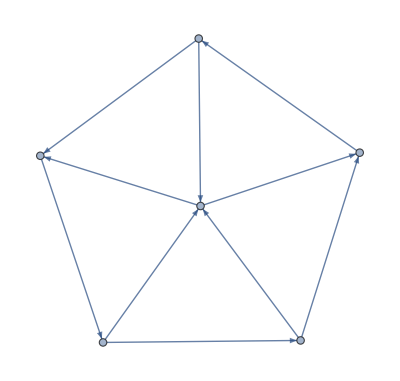
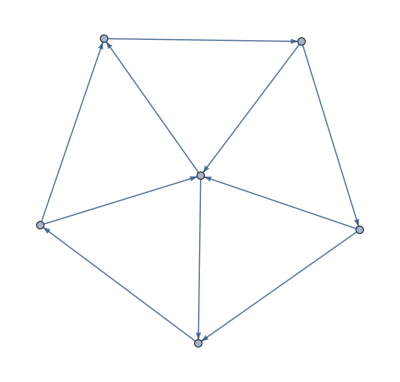
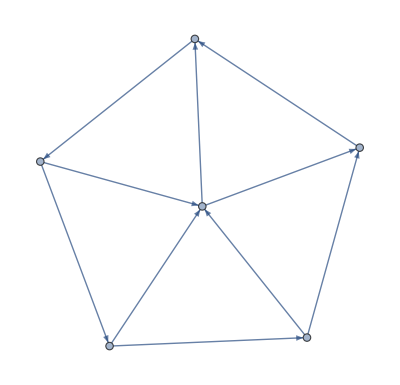
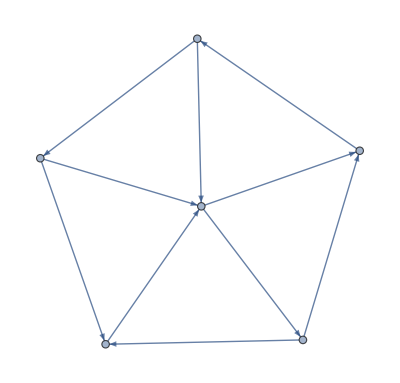

```mathematica
Map[g2,{96,104,117,119,168,183,200,201,211,215,224,232,243,247,296,311,328,343,360,375,391,392,394,407,424,439,455,456,457,471,552,566,567,568,584,599,616,629,631,632,648,663,680,695,712,727,776,780,791,799,808,812,822,823,840,855,904,906,919,927}]
```

```mathematica
Select[Range[2^10],CondQ[AdjacencyGraph[g0[PadLeft[IntegerDigits[#,2],10]]]]&]
```

{96,97,104,112,113,116,117,119,160,162,163,168,170,176,178,179,182,183,193,195,200,201,203,209,211,215,224,225,227,232,240,241,243,247,288,292,294,295,296,300,302,308,310,311,321,325,327,328,329,332,333,335,341,343,352,353,356,357,359,360,364,372,373,375,387,391,392,394,395,398,399,407,416,418,419,422,423,424,426,430,438,439,449,451,455,456,457,459,463,471,552,560,564,566,567,568,572,574,584,585,593,597,599,600,601,604,605,607,616,624,625,628,629,631,632,636,648,650,651,659,663,664,666,667,670,671,680,682,688,690,691,694,695,696,698,702,712,713,715,721,723,727,728,729,731,735,776,780,782,783,791,796,798,799,808,812,814,820,822,823,828,830,840,841,844,845,847,853,855,860,861,863,904,906,907,910,911,919,926,927}

```mathematica
signedplot[graph_]:=Block[{vlist=Table[i->(Piecewise[{{")+(", VertexOutDegree[graph,i]>VertexInDegree[graph,i]}, {"(-)", VertexOutDegree[graph,i]<VertexInDegree[graph,i]}, {".", VertexOutDegree[graph,i]==VertexInDegree[graph,i]}}]),{i,1,Length[VertexList[graph]]}]},Graph[EdgeList[graph],VertexLabels->vlist,VertexSize->Small]]
```

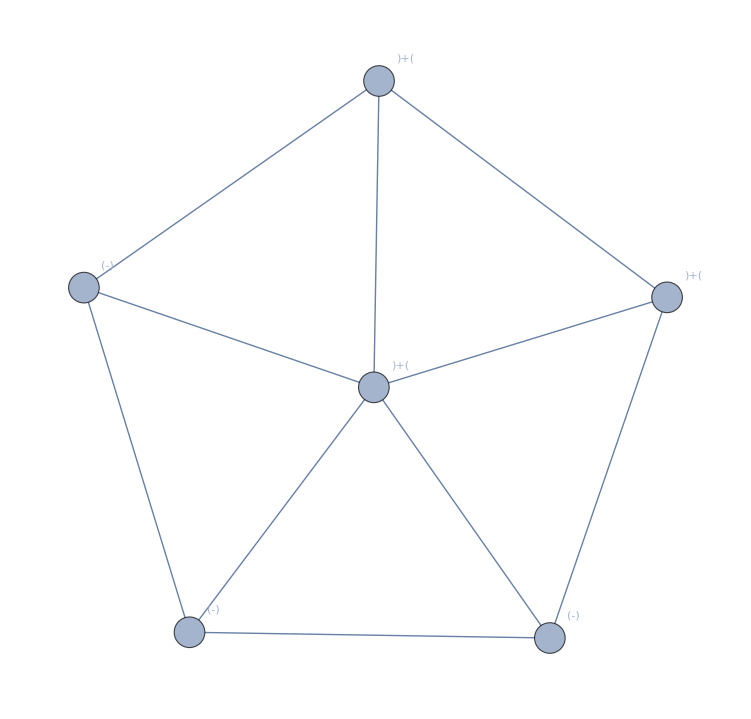

```mathematica
signedplot[-Graphics-]
```

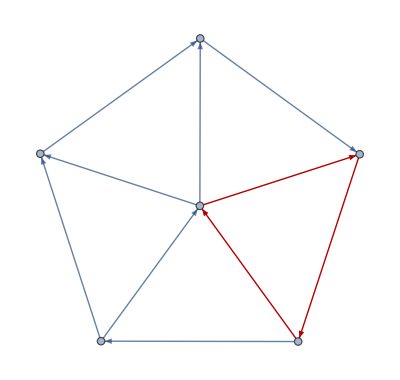
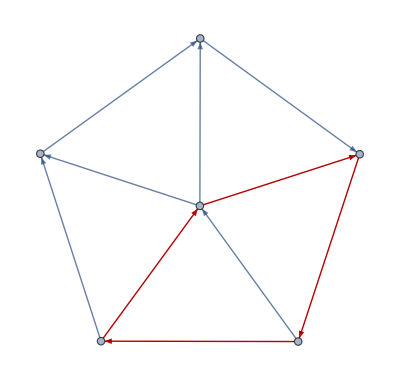
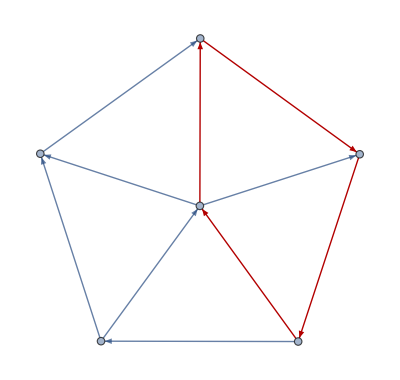
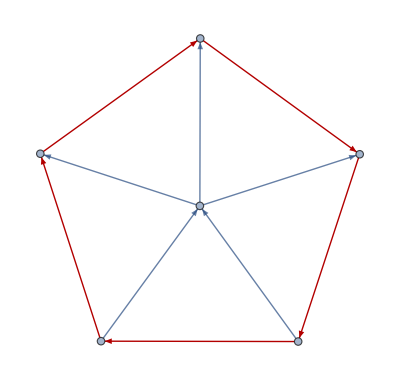
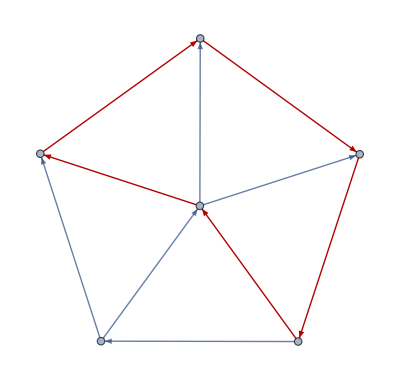
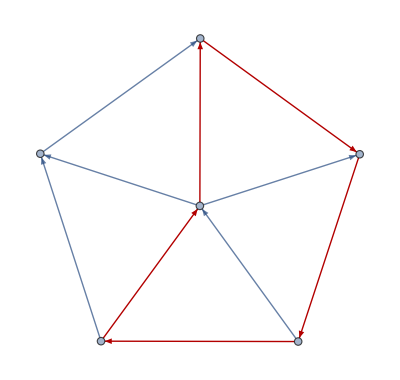
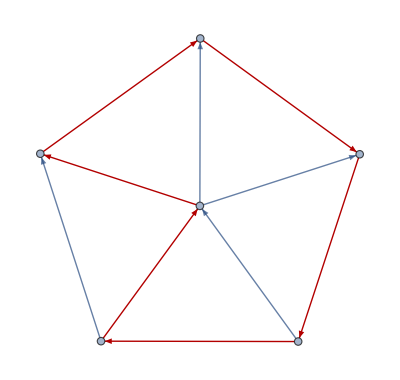

```mathematica
Map[HighlightGraph[-Graphics-,#]&,FindCycle[-Graphics-,∞,All]]
```

```mathematica
Graph[{1->5,1->6,2->1,3->1,3->2,4->1,4->3,5->4,6->2,6->5},VertexLabels->{1
```

```mathematica
VertexLabels->{1->place[{Above,After,Below,Before}],3->place[{Left,Top,Right,Bottom}]}
```

```mathematica
Map[signedplot,Out[170]]
```

```mathematica
Length[Out[170]]
```

60

```mathematica
Length[DeleteDuplicates[Out[170],IsomorphicGraphQ]]
```

6

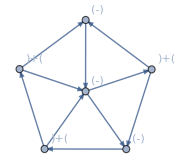
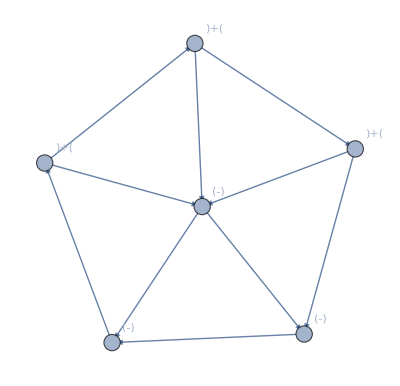
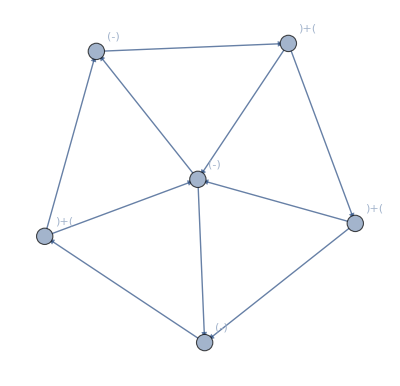
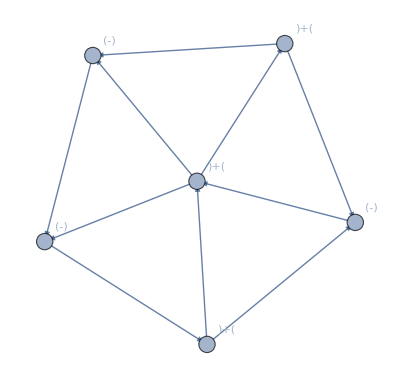
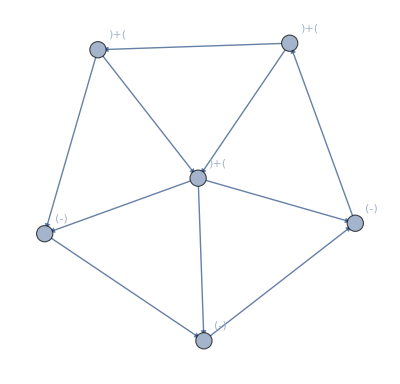
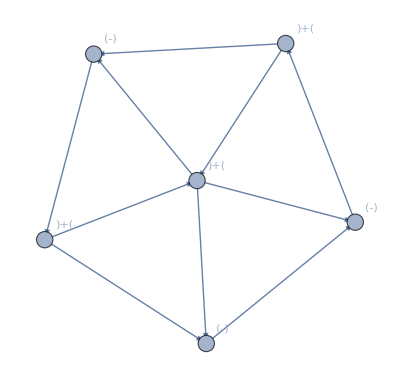

```mathematica
Map[signedplot,DeleteDuplicates[Out[170],IsomorphicGraphQ]]
```

```mathematica
esigns[graph_]:=
(*Map[Piecewise[{{+2, #[[1]]==+1&&#[[2]]==+1}, {-1, #[[1]]==+1&&#[[2]]==-1}, {1, #[[1]]==-1&&#[[2]]==+1}, {-2, #[[1]]==-1&&#[[2]]==-1}}]&,*)Map[{√(VertexOutDegree[graph,#[[1]]]-VertexInDegree[graph,#[[1]]]),√(VertexOutDegree[graph,#[[2]]]-VertexInDegree[graph,#[[2]]])}&,EdgeList[graph]]
```

```mathematica
Map[esigns[#]&,DeleteDuplicates[Out[170],IsomorphicGraphQ]]//Column
```

{{ⅈ,ⅈ},{ⅈ,1},{ⅈ,ⅈ},{1,ⅈ},{1,ⅈ},{1,ⅈ},{1,1},{ⅈ,1},{1,ⅈ},{1,ⅈ}}
{{ⅈ,ⅈ},{ⅈ,ⅈ},{1,ⅈ},{1,ⅈ},{1,ⅈ},{1,1},{1,ⅈ},{1,1},{ⅈ,1},{ⅈ,ⅈ}}
{{ⅈ,ⅈ},{ⅈ,ⅈ},{1,ⅈ},{1,ⅈ},{1,ⅈ},{1,1},{ⅈ,1},{1,ⅈ},{1,ⅈ},{ⅈ,1}}
{{1,ⅈ},{1,ⅈ},{1,1},{ⅈ,1},{1,1},{1,ⅈ},{ⅈ,1},{ⅈ,ⅈ},{1,ⅈ},{1,ⅈ}}
{{1,ⅈ},{1,ⅈ},{1,ⅈ},{1,1},{1,ⅈ},{1,1},{1,1},{ⅈ,1},{ⅈ,ⅈ},{ⅈ,ⅈ}}
{{1,ⅈ},{1,ⅈ},{1,ⅈ},{1,1},{1,ⅈ},{ⅈ,1},{1,1},{1,ⅈ},{ⅈ,1},{ⅈ,ⅈ}}